# Visualization of the orbits of Venus and Earth

It helps immeasurably to make a picture so you can see the problem’s geometry.

I’m going to work through everything in symbolic form before plugging in any numbers. The “plugging in” can be done using Mathematica transformation rule; here are transformation rules for the orbital parameters in this problem. Distances are measured in AU, times in years, angles in radians, speeds in km/s.

```mathematica
orbitalParameters = {
Subscript[a, v]->0.72,
Subscript[a, e]->1.0, 
Subscript[T, e]->1.0,
Subscript[T, v]->224.7/365.25,
Subscript[v, v]->35, 
Subscript[v, e]->30}
```

{a_v→0.72,a_e→1.,T_e→1.,T_v→0.615195,v_v→35,v_e→30}

Write functions for the angular positions of the planets as functions of time

```mathematica
Subscript[ϕ, e][t_]=2Pi t/Subscript[T, e];
```

```mathematica
Subscript[ϕ, v][t_]=2 Pi t/Subscript[T, v];
```

Write functions for the position vectors of the planets as functions of time

```mathematica
Subscript[r, v][t_]=Subscript[a, v]{Cos[Subscript[ϕ, v][t]],Sin[Subscript[ϕ, v][t]]}
```

{a_v cos((2 π t)/T_v),a_v sin((2 π t)/T_v)}

{a_v cos((2 π t)/T_v),a_v sin((2 π t)/T_v)}

{a_v cos((2 π t)/T_v),a_v sin((2 π t)/T_v)}

```mathematica
Subscript[r, e][t_]=Subscript[a, e]{Cos[Subscript[ϕ, e][t]],Sin[Subscript[ϕ, e][t]]}
```

{a_e cos((2 π t)/T_e),a_e sin((2 π t)/T_e)}

{a_e cos((2 π t)/T_e),a_e sin((2 π t)/T_e)}

{a_e cos((2 π t)/T_e),a_e sin((2 π t)/T_e)}

Draw the Sun, planets, their orbits, and position vectors at time t

```mathematica
drawit[t_]:=Graphics[{
{PointSize[0.03],Point[{0,0}]}, (* Sun *)
Circle[{0,0},Subscript[a, e]],(* Earth's orbit *)
Circle[{0,0},Subscript[a, v]], (* Venus's orbit *)
{PointSize[0.03],Point[Subscript[r, v][t]]}, (* Venus *)
{PointSize[0.03],Point[Subscript[r, e][t]]},(* Earth *)
Arrow[{{0,0},Subscript[r, e][t]}], (* pos vec for Earth *)
Arrow[{{0,0},Subscript[r, v][t]}],(* pos vec for Venus *)
Arrow[{Subscript[r, e][t],Subscript[r, v][t]}]
 (* displacement btw E and V *)
}
(* Apply the transformation rule to plug in numbers *)/.orbitalParameters
]
```

Draw at a particular time (0.1 years in this example)

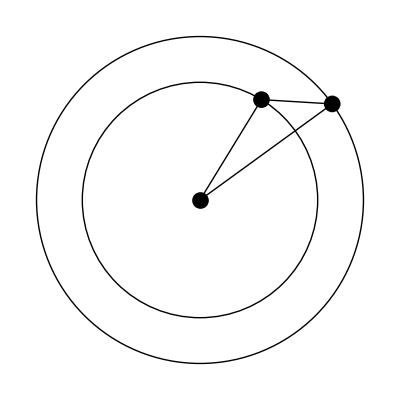

```mathematica
drawit[0.1]
```

Here’s a nicely labeled version of that picture (done interactively using the drawing tools).

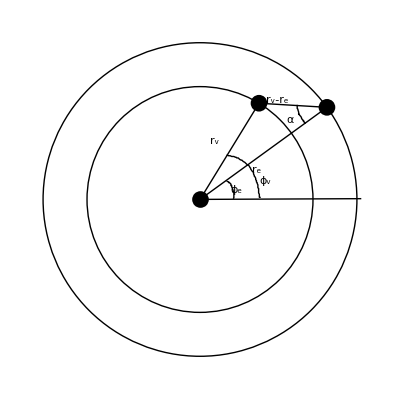

-Graphics-

You can make a movie showing the orbital motion

```mathematica
Animate[drawit[t],{t,0,4},AnimationRate->0.1,AnimationRunning->False]
```

### Part (a) Calculation of the apparent angle between Venus and the Sun as seen from Earth

See solution notes for how to compute this using a dot product between r_e and r_e-r_v.

```mathematica
Subscript[r, ev][t_]=Subscript[r, v][t]-Subscript[r, e][t]
```

{a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e),a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)}

{a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e),a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)}

{a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e),a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)}

```mathematica
cosAlpha[t_]=(-Subscript[r, e][t].Subscript[r, ev][t])/Sqrt[Subscript[r, e][t].Subscript[r, e][t]]/Sqrt[Subscript[r, ev][t].Subscript[r, ev][t]]
```

(a_e (-cos((2 π t)/T_e)) (a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))-a_e sin((2 π t)/T_e) (a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)))/(√(a_e^2 sin^2((2 π t)/T_e)+a_e^2 cos^2((2 π t)/T_e)) √((a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e))^2+(a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))^2))

(a_e (-cos((2 π t)/T_e)) (a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))-a_e sin((2 π t)/T_e) (a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)))/(√(a_e^2 sin^2((2 π t)/T_e)+a_e^2 cos^2((2 π t)/T_e)) √((a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e))^2+(a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))^2))

(a_e (-cos((2 π t)/T_e)) (a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))-a_e sin((2 π t)/T_e) (a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e)))/(√(a_e^2 sin^2((2 π t)/T_e)+a_e^2 cos^2((2 π t)/T_e)) √((a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e))^2+(a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))^2))

That’s a hideous mess, so run FullSimplify on it.

```mathematica
FullSimplify[cosAlpha[t]]
```

(a_e (a_e-a_v cos(2 π t (1/T_e-1/T_v))))/(√(a_e^2) √(-2 a_e a_v cos(2 π t (1/T_e-1/T_v))+a_e^2+a_v^2))

That’s exactly the same as what I found doing the calculation by hand.

Plot the angle (in degrees) over five years

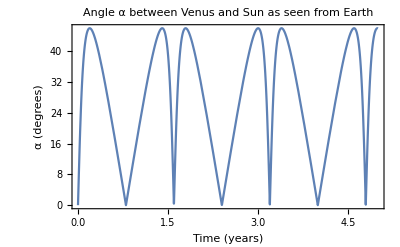

```mathematica
Plot[ArcCos[cosAlpha[t]]*180/Pi /. orbitalParameters,{t,0,5},
Frame->True,FrameLabel->{"Time (years)", "α (degrees)"},PlotLabel->"Angle α between Venus and Sun as seen from Earth"]
```

#### Part (a.ii)

See solution notes for the explanation of how to find the “maximum elongation” of Venus using very simple trigonometry. Here’s the calculation step:

```mathematica
ArcSin[Subscript[a, v]/Subscript[a, e]]180/Pi /. orbitalParameters
```

46.0545

46.0545

46.0545

### Part (b) Calculation of the radial velocity of Venus as measured from Earth

We’ll need unit vectors tangential to both orbits.

```mathematica
Subscript[ϕ̂, e][t_]={-Sin[Subscript[ϕ, e][t]],Cos[Subscript[ϕ, e][t]]}
```

{-sin((2 π t)/T_e),cos((2 π t)/T_e)}

{-sin((2 π t)/T_e),cos((2 π t)/T_e)}

{-sin((2 π t)/T_e),cos((2 π t)/T_e)}

```mathematica
Subscript[ϕ̂, v][t_]={-Sin[Subscript[ϕ, v][t]],Cos[Subscript[ϕ, v][t]]}
```

{-sin((2 π t)/T_v),cos((2 π t)/T_v)}

Find a unit vector parallel to the line of sight

```mathematica
Subscript[r̂, ev][t_]=Subscript[r, ev][t]/Sqrt[Subscript[r, ev][t].Subscript[r, ev][t]]//FullSimplify
```

{(a_v cos((2 π t)/T_v)-a_e cos((2 π t)/T_e))/(√(-2 a_e a_v cos(2 π t (1/T_e-1/T_v))+a_e^2+a_v^2)),(a_v sin((2 π t)/T_v)-a_e sin((2 π t)/T_e))/(√(-2 a_e a_v cos(2 π t (1/T_e-1/T_v))+a_e^2+a_v^2))}

Compute the radial velocity

```mathematica
Subscript[v, r][t_]=Subscript[r̂, ev][t].(Subscript[v, v] Subscript[ϕ̂, v][t]-Subscript[v, e] Subscript[ϕ̂, e][t])//FullSimplify
```

((a_v v_e-v_v a_e) sin(2 π t (1/T_e-1/T_v)))/(√(-2 a_e a_v cos(2 π t (1/T_e-1/T_v))+a_e^2+a_v^2))

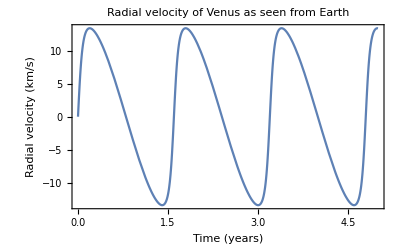

```mathematica
Plot[Subscript[v, r][t]/.orbitalParameters,{t,0,5},
Frame->True,FrameLabel->{"Time (years)", "Radial velocity (km/s)"},PlotLabel->"Radial velocity of Venus as seen from Earth"]
```

#### Part (b.ii)

See the solution notes for an explanation. Here is the numerical calculation.

```mathematica
Subscript[v, max]=Subscript[v, v]-Subscript[a, v]/Subscript[a, e] Subscript[v, e]/. orbitalParameters
```

13.4